```mathematica
PolyhedronData["Properties"]
```

{AdjacentFaceIndices,AlternateNames,AlternateStandardNames,Amphichiral,Antiprism,Archimedean,ArchimedeanDual,Centroid,Chiral,Circumcenter,Circumradius,Circumsphere,Classes,Compound,Concave,Convex,Cuboid,DefaultOrientation,Deltahedron,DihedralAngleRules,DihedralAngles,Dipyramid,DualCompound,DualName,DualScale,EdgeCount,EdgeIndices,EdgeLengths,Edges,Equilateral,FaceCount,FaceCountRules,FaceIndices,Faces,GeneralizedDiameter,Hypercube,Image,Incenter,InertiaTensor,Information,Inradius,Insphere,Johnson,KeplerPoinsot,Midcenter,Midradius,Midsphere,Name,NetCoordinates,NetCount,NetEdgeIndices,NetEdges,NetFaceIndices,NetFaces,NetImage,NotationRules,Orientations,Orthotope,Platonic,PolyhedronIndices,Prism,Pyramid,Quasiregular,RectangularParallelepiped,RegionFunction,Rhombohedron,Rigid,SchlaefliSymbol,SelfDual,Shaky,Simplex,SkeletonCoordinates,SkeletonGraphName,SkeletonImage,SkeletonRules,SpaceFilling,StandardName,StandardNames,Stellation,StellationCount,SurfaceArea,SymmetryGroupString,Uniform,UniformDual,VertexCoordinates,VertexCount,VertexIndices,Volume,WythoffSymbol,Zonohedron}

```mathematica
PolyhedronData["Icosahedron", "EdgeIndices"]
```

{{1,3},{1,5},{1,6},{1,9},{1,10},{2,4},{2,7},{2,8},{2,11},{2,12},{3,7},{3,8},{3,9},{3,10},{4,5},{4,6},{4,11},{4,12},{5,6},{5,9},{5,11},{6,10},{6,12},{7,8},{7,9},{7,11},{8,10},{8,12},{9,11},{10,12}}

```mathematica
PolyhedronData["Icosahedron", "NetEdges"]
```

GraphicsComplex[{{1,0},{2,0},{3,0},{4,0},{5,0},{1/2,(√3)/2},{3/2,(√3)/2},{5/2,(√3)/2},{7/2,(√3)/2},{9/2,(√3)/2},{11/2,(√3)/2},{0,√3},{1,√3},{2,√3},{3,√3},{4,√3},{5,√3},{1/2,(3 √3)/2},{3/2,(3 √3)/2},{5/2,(3 √3)/2},{7/2,(3 √3)/2},{9/2,(3 √3)/2}},Line[{{1,6},{1,7},{2,7},{2,8},{3,8},{3,9},{4,9},{4,10},{5,10},{5,11},{6,7},{6,12},{6,13},{7,8},{7,13},{7,14},{8,9},{8,14},{8,15},{9,10},{9,15},{9,16},{10,11},{10,16},{10,17},{11,17},{12,13},{12,18},{13,14},{13,18},{13,19},{14,15},{14,19},{14,20},{15,16},{15,20},{15,21},{16,17},{16,21},{16,22},{17,22}}]]

```mathematica
PolyhedronData["Icosahedron", "EdgeCount"]
```

30

```mathematica
PolyhedronData["Icosahedron", "NetCount"]
```

43380

```mathematica
PolyhedronData["Icosahedron", "NetEdgeIndices"]
```

{{1,6},{1,7},{2,7},{2,8},{3,8},{3,9},{4,9},{4,10},{5,10},{5,11},{6,7},{6,12},{6,13},{7,8},{7,13},{7,14},{8,9},{8,14},{8,15},{9,10},{9,15},{9,16},{10,11},{10,16},{10,17},{11,17},{12,13},{12,18},{13,14},{13,18},{13,19},{14,15},{14,19},{14,20},{15,16},{15,20},{15,21},{16,17},{16,21},{16,22},{17,22}}

```mathematica
PolyhedronData["Icosahedron", "StellationCount"]
```

58

Attributes[Graphics]={Protected,ReadProtected}
 
Options[Graphics]={AlignmentPoint→Center,AspectRatio→Automatic,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},Method→Automatic,PlotLabel→None,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,Ticks→Automatic,TicksStyle→{}}

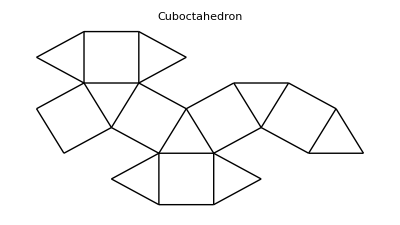
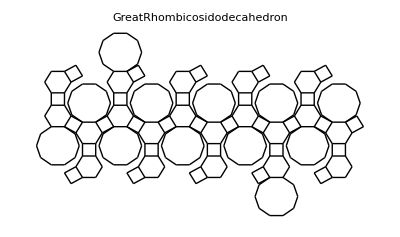
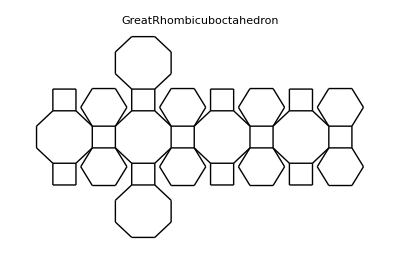
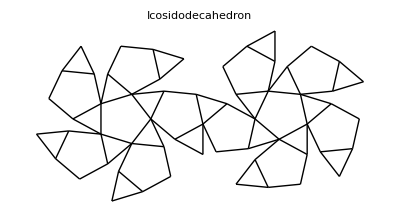
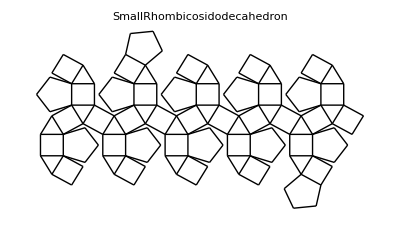
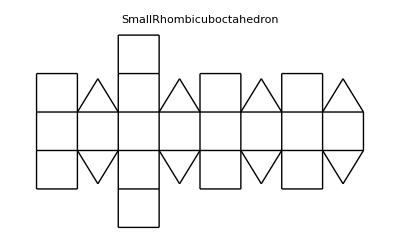
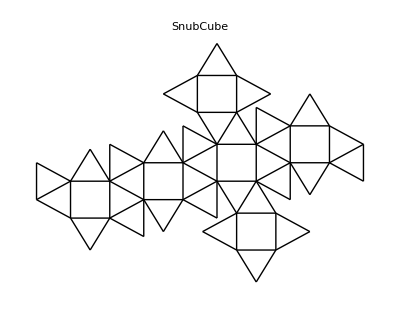
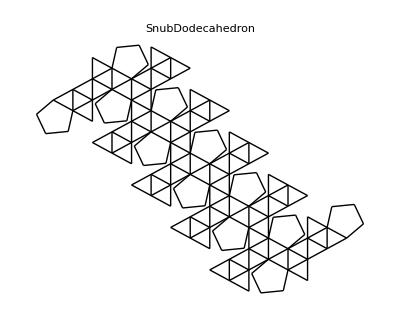

```mathematica
Map[Graphics[PolyhedronData[#, "NetEdges"], PlotLabel -> #] &, PolyhedronData["Archimedean"]]
```

```mathematica
PolyhedronData["Archimedean"]
```

{Cuboctahedron,GreatRhombicosidodecahedron,GreatRhombicuboctahedron,Icosidodecahedron,SmallRhombicosidodecahedron,SmallRhombicuboctahedron,SnubCube,SnubDodecahedron,TruncatedCube,TruncatedDodecahedron,TruncatedIcosahedron,TruncatedOctahedron,TruncatedTetrahedron}

```mathematica
Plot[PolyhedronData["Icosahedron", "NetEdges"]]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[PolyhedronData[Icosahedron,NetEdges]]

```mathematica
Manipulate[name, {"bob", "cindy"}]
```

Manipulate::vsform: Manipulate argument bobcindy does not have the correct form for a variable specification.

```mathematica
Manipulate[name,{name, {"bob","cindy"}, ControlType -> PopupMenu}]
```

```mathematica
PolyhedronData[All]
```

{{Antiprism,4},{Antiprism,5},{Antiprism,6},{Antiprism,7},{Antiprism,8},{Antiprism,9},{Antiprism,10},AugmentedDodecahedron,AugmentedHexagonalPrism,AugmentedPentagonalPrism,AugmentedSphenocorona,AugmentedTriangularPrism,AugmentedTridiminishedIcosahedron,AugmentedTruncatedCube,AugmentedTruncatedDodecahedron,AugmentedTruncatedTetrahedron,BiaugmentedPentagonalPrism,BiaugmentedTriangularPrism,BiaugmentedTruncatedCube,BigyrateDiminishedRhombicosidodecahedron,Bilunabirotunda,CsaszarPolyhedron,Cube,CubeFiveCompound,CubeFourCompound,CubeOctahedronCompound,CubeOctahedronFiveCompound,CubeOctahedronThreeCompound,CubeSixCompound,CubeTenCompound,CubeThreeCompound,CubeTwoCompound,Cuboctahedron,DeltoidalHexecontahedron,DeltoidalIcositetrahedron,DiminishedRhombicosidodecahedron,{Dipyramid,3},{Dipyramid,5},DisdyakisDodecahedron,DisdyakisTriacontahedron,Disphenocingulum,Dodecahedron,DodecahedronFiveCompound,DodecahedronIcosahedronCompound,DodecahedronSixCompound,DodecahedronSmallTriambicIcosahedronCompound,DodecahedronTwoCompound,DuerersSolid,Echidnahedron,ElongatedDodecahedron,ElongatedPentagonalCupola,ElongatedPentagonalDipyramid,ElongatedPentagonalGyrobicupola,ElongatedPentagonalGyrobirotunda,ElongatedPentagonalGyrocupolarotunda,ElongatedPentagonalOrthobicupola,ElongatedPentagonalOrthobirotunda,ElongatedPentagonalOrthocupolarotunda,ElongatedPentagonalPyramid,ElongatedPentagonalRotunda,ElongatedSquareCupola,ElongatedSquareDipyramid,ElongatedSquareGyrobicupola,ElongatedSquarePyramid,ElongatedTriangularCupola,ElongatedTriangularDipyramid,ElongatedTriangularGyrobicupola,ElongatedTriangularOrthobicupola,ElongatedTriangularPyramid,EschersSolid,GreatDodecahedron,GreatIcosahedron,GreatRhombicosidodecahedron,GreatRhombicTriacontahedron,GreatRhombicuboctahedron,GreatStellatedDodecahedron,GyrateBidiminishedRhombicosidodecahedron,GyrateRhombicosidodecahedron,Gyrobifastigium,GyroelongatedPentagonalBicupola,GyroelongatedPentagonalBirotunda,GyroelongatedPentagonalCupola,GyroelongatedPentagonalCupolarotunda,GyroelongatedPentagonalPyramid,GyroelongatedPentagonalRotunda,GyroelongatedSquareBicupola,GyroelongatedSquareCupola,GyroelongatedSquareDipyramid,GyroelongatedSquarePyramid,GyroelongatedTriangularBicupola,GyroelongatedTriangularCupola,Hebesphenomegacorona,HexagonalPrismSixCompound,Icosahedron,IcosahedronFiveCompound,IcosahedronSixCompound,IcosahedronTwoCompound,Icosidodecahedron,JessensOrthogonalIcosahedron,MathematicaPolyhedron,MetabiaugmentedDodecahedron,MetabiaugmentedHexagonalPrism,MetabiaugmentedTruncatedDodecahedron,MetabidiminishedIcosahedron,MetabidiminishedRhombicosidodecahedron,MetabigyrateRhombicosidodecahedron,MetagyrateDiminishedRhombicosidodecahedron,Octahedron,OctahedronFiveCompound,OctahedronFourCompound,OctahedronTenCompound,OctahedronThreeCompound,ParabiaugmentedDodecahedron,ParabiaugmentedHexagonalPrism,ParabiaugmentedTruncatedDodecahedron,ParabidiminishedRhombicosidodecahedron,ParabigyrateRhombicosidodecahedron,ParagyrateDiminishedRhombicosidodecahedron,PentagonalCupola,PentagonalGyrobicupola,PentagonalGyrocupolarotunda,PentagonalHexecontahedron,PentagonalIcositetrahedron,PentagonalOrthobicupola,PentagonalOrthobirotunda,PentagonalOrthocupolarotunda,PentagonalRotunda,PentakisDodecahedron,{Prism,3},{Prism,5},{Prism,6},{Prism,7},{Prism,8},{Prism,9},{Prism,10},{Pyramid,4},{Pyramid,5},RhombicDodecahedron,{RhombicDodecahedronStellation,2},RhombicEnneacontahedron,RhombicHexecontahedron,RhombicIcosahedron,RhombicTriacontahedron,SmallRhombicosidodecahedron,SmallRhombicuboctahedron,SmallStellatedDodecahedron,SmallTriakisOctahedron,SmallTriambicIcosahedron,SnubCube,SnubDisphenoid,SnubDodecahedron,SnubSquareAntiprism,Sphenocorona,Sphenomegacorona,SquareCupola,SquareGyrobicupola,SquareOrthobicupola,SquashedDodecahedron,StellaOctangula,SzilassiPolyhedron,Tetrahedron,TetrahedronFiveCompound,{TetrahedronFourCompound,1},{TetrahedronFourCompound,2},{TetrahedronFourCompound,3},TetrahedronSixCompound,TetrahedronTenCompound,TetrahedronThreeCompound,TetrahedronTwoCompound,TetrakisHexahedron,TriakisIcosahedron,TriakisTetrahedron,TriangularCupola,TriangularHebesphenorotunda,TriangularOrthobicupola,TriaugmentedDodecahedron,TriaugmentedHexagonalPrism,TriaugmentedTriangularPrism,TriaugmentedTruncatedDodecahedron,TridiminishedIcosahedron,TridiminishedRhombicosidodecahedron,TrigyrateRhombicosidodecahedron,TruncatedCube,TruncatedDodecahedron,TruncatedIcosahedron,TruncatedOctahedron,TruncatedTetrahedron}

```mathematica
PolyhedronData["classes"]
```

PolyhedronData::notdef: PolyhedronData has no value associated with the specified argument(s).

```mathematica
PolyhedronData["Classes"]
```

{Amphichiral,Antiprism,Archimedean,ArchimedeanDual,Chiral,Compound,Concave,Convex,Cuboid,Deltahedron,Dipyramid,Equilateral,Hypercube,Johnson,KeplerPoinsot,Orthotope,Platonic,Prism,Pyramid,Quasiregular,RectangularParallelepiped,Rhombohedron,Rigid,SelfDual,Shaky,Simplex,SpaceFilling,Stellation,Uniform,UniformDual,Zonohedron}

```mathematica
PolyhedronData["Cube"]
```

-Graphics3D-

```mathematica
Manipulate[Manipulate[Column[{
PolyhedronData[polyhedron], 
PolyhedronData[polyhedron, "NetImage"],
 PolyhedronData[polyhedron,"DualName"],
PolyhedronData[PolyhedronData[polyhedron, "DualName"]],
PolyhedronData[PolyhedronData[polyhedron, "DualName"],"NetImage"]
}], 
{polyhedron, PolyhedronData[class], ControlType -> PopupMenu}],{{class,"Platonic"}, PolyhedronData["Classes"]}]
```

PolyhedronData::notdef: PolyhedronData has no value associated with the specified argument(s).

```mathematica
{edgeCoordinates,edgeIndices}=StringReplace[ToString/@(List@@N[PolyhedronData["Tetrahedron","NetEdges"]]/.Line->Sequence),{"{"->"[","}"->"]"}]
```

{[[0., 0.], [0.5, 0.866025], [1., 0.], [1., 1.73205], [1.5, 0.866025], [2., 0.]],[[1, 2], [1, 3], [2, 3], [2, 4], [2, 5], [3, 5], [3, 6], [4, 5], [5, 6]]}

```mathematica
Map[PolyhedronData[#, "NetEdges"] &, PolyhedronData["Platonic"]];
```

```mathematica
StringReplace[ToString/@ Append[{"\"Tetrahedron\" : "}, (List@@N[PolyhedronData["Tetrahedron","NetEdges"]]/.Line->Sequence)],{"{"->"[","}"->"]"}]
```

{"Tetrahedron" : ,[[[0., 0.], [0.5, 0.866025], [1., 0.], [1., 1.73205], [1.5, 0.866025], [2., 0.]], [[1, 2], [1, 3], [2, 3], [2, 4], [2, 5], [3, 5], [3, 6], [4, 5], [5, 6]]]}

```mathematica
a=StringReplace[ToString/@(List@@N[PolyhedronData["Tetrahedron","NetEdges"]]/.Line->Sequence),{"{"->"[","}"->"]"}]
```

{[[0., 0.], [0.5, 0.866025], [1., 0.], [1., 1.73205], [1.5, 0.866025], [2., 0.]],[[1, 2], [1, 3], [2, 3], [2, 4], [2, 5], [3, 5], [3, 6], [4, 5], [5, 6]]}

```mathematica
Prepend[{"\'edgeCoordinates\' : ", "a"}, a]
```

{{[[0., 0.], [0.5, 0.866025], [1., 0.], [1., 1.73205], [1.5, 0.866025], [2., 0.]],[[1, 2], [1, 3], [2, 3], [2, 4], [2, 5], [3, 5], [3, 6], [4, 5], [5, 6]]},\'edgeCoordinates\' : ,a}

```mathematica
Flatten[{PolyhedronData["Platonic"], PolyhedronData["Archimedean"]}]
```

{Cube,Dodecahedron,Icosahedron,Octahedron,Tetrahedron,Cuboctahedron,GreatRhombicosidodecahedron,GreatRhombicuboctahedron,Icosidodecahedron,SmallRhombicosidodecahedron,SmallRhombicuboctahedron,SnubCube,SnubDodecahedron,TruncatedCube,TruncatedDodecahedron,TruncatedIcosahedron,TruncatedOctahedron,TruncatedTetrahedron}

```mathematica
edgeCoordinates
```

[[0., 0.], [0.5, 0.866025], [1., 0.], [1., 1.73205], [1.5, 0.866025], [2., 0.]]

```mathematica
ToString["'" <> # <> "' : " <> ("{'edgeCoordinates' : " <> #1  <> ", 'edgeIndices' : " <> #2 <> "}"& @@StringReplace[ToString/@(List@@N[PolyhedronData[#,"NetEdges"]]/.Line->Sequence),{"{"->"[","}"->"]"}]) & /@ Flatten[{PolyhedronData["Platonic"], PolyhedronData["Archimedean"]}]
];
```

```mathematica
ToString[%]
```

{'Tetrahedron' : {'netEdges' : [[0., 0.], [0.5, 0.866025], [1., 0.], [1., 1.73205], [1.5, 0.866025], [2., 0.]], 'edgeCoordinates' : [[1, 2], [1, 3], [2, 3], [2, 4], [2, 5], [3, 5], [3, 6], [4, 5], [5, 6]]}, 'Cube' : {'netEdges' : [[0., 1.], [0., 2.], [1., 0.], [1., 1.], [1., 2.], [1., 3.], [2., 0.], [2., 1.], [2., 2.], [2., 3.], [3., 1.], [3., 2.], [4., 1.], [4., 2.]], 'edgeCoordinates' : [[1, 2], [1, 4], [2, 5], [3, 4], [3, 7], [4, 5], [4, 8], [5, 6], [5, 9], [6, 10], [7, 8], [8, 9], [8, 11], [9, 10], [9, 12], [11, 12], [11, 13], [12, 14], [13, 14]]}}

```mathematica
Manipulate[
Column[
Map[
Row[{#, PolyhedronData[#], PolyhedronData[#, "NetImage"]}] &, 
PolyhedronData[class]
]
],
{{class,"Platonic"}, PolyhedronData["Classes"]}]
```

```mathematica
Graphics3D[PolyhedronData["RhombicHexecontahedron", "Edges"]]
```

-Graphics3D-

```mathematica
PolyhedronData["Cube", "Edges"]
```

GraphicsComplex[{{-1/2,-1/2,-1/2},{-1/2,-1/2,1/2},{-1/2,1/2,-1/2},{-1/2,1/2,1/2},{1/2,-1/2,-1/2},{1/2,-1/2,1/2},{1/2,1/2,-1/2},{1/2,1/2,1/2}},Line[{{1,2},{1,3},{1,5},{2,4},{2,6},{3,4},{3,7},{4,8},{5,6},{5,7},{6,8},{7,8}}]]

```mathematica
Graphics3D[GraphicsComplex[{{1,1,1}, {0,0,0}},{Line[{{1,2}}],Text["test1",1], Text["test2", 2]}]]
```

-Graphics3D-

```mathematica
points
```

{{-1/2,-1/2,-1/2},{-1/2,-1/2,1/2},{-1/2,1/2,-1/2},{-1/2,1/2,1/2},{1/2,-1/2,-1/2},{1/2,-1/2,1/2},{1/2,1/2,-1/2},{1/2,1/2,1/2}}

```mathematica
edges
```

{{1,2},{1,3},{1,5},{2,4},{2,6},{3,4},{3,7},{4,8},{5,6},{5,7},{6,8},{7,8}}

```mathematica
Length[points]
```

8

```mathematica
Range[Length[points]]
```

{1,2,3,4,5,6,7,8}

```mathematica
InputForm[PolyhedronData["Cube"]]
```

Graphics3D[GraphicsComplex[{{-1/2, -1/2, -1/2}, {-1/2, -1/2, 1/2}, {-1/2, 1/2, -1/2}, {-1/2, 1/2, 1/2}, {1/2, -1/2, -1/2}, {1/2, -1/2, 1/2}, 
   {1/2, 1/2, -1/2}, {1/2, 1/2, 1/2}}, Polygon[{{8, 4, 2, 6}, {8, 6, 5, 7}, {8, 7, 3, 4}, {4, 3, 1, 2}, {1, 3, 7, 5}, {2, 1, 5, 6}}]]]

```mathematica
PolyhedronData["Cube", "Faces"]
```

GraphicsComplex[{{-1/2,-1/2,-1/2},{-1/2,-1/2,1/2},{-1/2,1/2,-1/2},{-1/2,1/2,1/2},{1/2,-1/2,-1/2},{1/2,-1/2,1/2},{1/2,1/2,-1/2},{1/2,1/2,1/2}},Polygon[{{8,4,2,6},{8,6,5,7},{8,7,3,4},{4,3,1,2},{1,3,7,5},{2,1,5,6}}]]

```mathematica
gc =PolyhedronData["RhombicHexecontahedron", "Faces"];
points = First[gc];
faces = First[Last[gc]];
Graphics3D[GraphicsComplex[points, {Polygon[faces], Map[Style[Text[#, #], Bold] &, Range[Length[points]]]}], Boxed->True]
```

-Graphics3D-

```mathematica
diff[x_, y_] := Sqrt[(N[points[[x]]-points[[y]]]^2) /. List -> Plus]
```

```mathematica
??Plus
```

x+y+z represents a sum of terms.

Attributes[Plus]={Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}
 
Default[Plus]:=0

```mathematica
Plus[{1,2,3}]
```

{1,2,3}

```mathematica
% /. List -> Plus
```

6

```mathematica
%[[1]]^2 + %[[3]]^2
```

1.10557

```mathematica
Sqrt[%]
```

1.05146